```mathematica
spectralEmbedPredictor[graph_,dim_ :4,k_ : 4]:=
Module[{L,evals,evecs,calculatedPoints, prediction,d, n, A},

(* Delete duplicate pairs and distances *)
deleteduplicates[pairs_, distances_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
{Delete[pairs,todelete], Delete[distances,todelete]}];

(* Compute all the distances and take the k smallest *)
brute[n_,points_, kval_,A_] := 
Module[{dists, inds, indarr, row, temp, max},
dists = DistanceMatrix[points] ;
max = Max[dists] * 10.;
dists = dists + max * A + LowerTriangularize[ConstantArray[max, Dimensions[A]]];
temp = Ordering[Flatten[dists], If[Length[dists] < kval, Length[dists], kval]];
inds = Do[Sow[getpoints[p, n]], {p,temp}]//Reap//Last//Last;
{inds, Flatten[dists][[temp]]}];

(* Finds the k closest points to each point in points *)
allclosest[nval_,points_, l_, A_] :=
Module[{range,inds,dists, count},
count = l;
If[nval ≤ count,count = nval-1];
 range= Range[nval];
inds = Nearest[points->range,points,count+1][[All, Range[2,count+1]]];
calcdist[i_,j_]:=EuclideanDistance[points[[i]],points[[inds[[i,j]]]]] + 100*A[[i,inds[[i,j]]]];
dists = N[Array[calcdist, {nval,count}]];
{dists, inds, count}];

(* gives coordinates from flattened array to nonflattened *)
getpoints[loc_, kval_]:=
Module[{a,b},
{a,b} = QuotientRemainder[loc +kval,kval];
If[b == 0,{a,b} = {a-1,b+kval}];
{a,b}];

(* checks which nodes need to run through the program again *)
counter[n_,pairs_,points_,l_] := 
Module[{set, counts, mask, return},
set = DeleteDuplicates[pairs];
counts = Do[Sow[Count[pairs,x]],{x,set}]//Reap//Last//Last;
mask = For[i=1,i<Length[set]+1,i++,If[counts[[i]] ≥ l, Sow[set[[i]]]]]//Reap//Last;
If[mask === {}, return = {{},{}}, return = {points[[mask//Last]], mask//Last}];
return];

(* the actually heart of the function *)
continue[n_,points_,kval_,l_, L_,A_] := 
Module[{dists, inds, npairs, bestkinds, pairs,  pdists, S,mask, sclosest, sdists, count, temp},
{dists, inds, count} = allclosest[n,points,l + IntegerPart[Max[L]], A];
npairs = 2*kval;
bestkinds = Do[Sow[getpoints[p, count]], {p,Ordering[Flatten[dists], npairs]}]//Reap//Last//Last;
pairs = ConstantArray[0,{npairs, 2}];
pairs[[All,1]] = bestkinds[[All,1]];
pairs[[All,2]] = Do[Sow[inds[[bestkinds[[x,1]],bestkinds[[x,2]]]]],{x,npairs}]//Reap//Last//Last;
{S,mask} = counter[n,pairs[[All,1]], points, l];
pdists = Do[Sow[dists[[bestkinds[[x]][[1]],bestkinds[[x]][[2]]]]],{x, Length[bestkinds]}]//Reap//Last//Last;
{pairs, pdists} = deleteduplicates[pairs, pdists];
{sclosest, sdists} = If[Length[mask] > 1, closest[S,kval, L[[mask, mask]], A[[mask, mask]]],{{},{}}];
temp = Do[Sow[mask[[sclosest[[i]]]]], {i,Length[sclosest]}]//Reap//Last;
If[temp === {}, pairs = pairs, pairs = Join[pairs, temp//Last]];
pdists = Join[pdists, sdists];
{pairs, pdists} = deleteduplicates[pairs, pdists];
{pairs,pdists}];

(* Check if k is such that it is just as fast to do brute force *)
closest[points_, kval_, L_,A_]:=
Module[{nval, l},
nval = Length[points];
l = Ceiling[4*kval/N[nval]];
If[nval===0, {{},{}},If[(nval*nval) ≤ (4*kval)|| nval ≤ l, brute[nval, points, kval, A], continue[nval,points,kval,l, L,A]]]];

d = dim + 1;
A = AdjacencyMatrix[graph];
L = N[KirchhoffMatrix[graph]];
evals = Reverse[N[Eigenvalues[L, -d]][[1;;d-1]]];
evecs = Reverse[N[Eigenvectors[L, -d]][[1;;d-1]]];
n = Length[L];
calculatedPoints = Transpose[evecs/Sqrt[evals]];
prediction  = closest[calculatedPoints, k, L,A];
prediction];
```

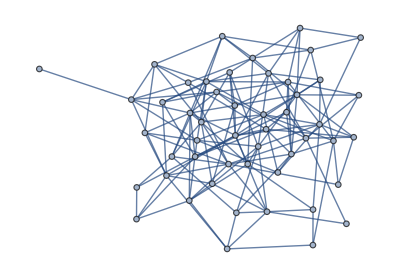

```mathematica
G = RandomGraph[{50,150}]
```

```mathematica
{prediction, distances} = spectralEmbedPredictor[g,4,k];
```

```mathematica
nodes  = VertexList[g];
nodes[[prediction]]
```

Part::pkspec1: The expression {{83,91},{56,71},{62,90},{126,150},{70,72},{62,83},{124,170},{62,91},{152,154},{76,140},{144,153},{83,90},{90,91},{159,166},{164,169},{46,47},{146,150},{140,176},{86,120},{51,57},«11»,{61,98},{136,173},{161,166},{78,150},{166,170},{126,144},{81,87},{78,126},{80,87},{132,133},{155,165},{124,159},{144,150},{145,153},{61,127},{132,171},{146,153},{159,170},{144,146},«481»} cannot be used as a part specification.

```mathematica
predictedlinks = dictionaryBackward[prediction, VertexList[g]];
```

```mathematica
predictedlinks
```

```mathematica
prediction
```

```mathematica
test
```

```mathematica
Intersection[toPredict, predictedLinks]
```

{}

```mathematica
Intersection[toPredict, predictedlinks]
```

{{1,76},{4,37},{6,30},{6,76},{8,35},{8,37},{8,38},{8,41},{8,60},{9,30},{9,50},{9,204},{10,30},{10,36},{10,40},{10,41},{10,60},{10,76},{11,76},{12,50},{13,50},{13,62},{17,76},{18,61},{19,30},{22,54},{24,50},{25,60},{26,43},{26,65},{31,45},{31,60},{32,50},{32,62},{32,127},{35,76},{36,45},{37,61},{38,61},{41,61},{43,76},{45,61},{46,61},{60,61},{60,76},{61,76}}

```mathematica
Intersection[predictedLinks, predictedlinks]
```

{{36,41},{78,79},{78,83},{79,83},{96,128},{96,149},{96,239},{96,240},{101,137},{101,236},{106,217},{106,219},{120,121},{128,149},{128,239},{128,240},{135,198},{137,168},{137,169},{137,170},{138,233},{138,234},{149,239},{149,240},{160,171},{160,173},{163,172},{163,221},{168,169},{168,170},{169,170},{171,173},{172,216},{178,179},{178,180},{178,181},{179,180},{179,181},{180,181},{182,185},{182,187},{184,186},{184,189},{185,187},{186,189},{196,197},{196,200},{197,200},{207,258},{210,256},{212,242},{212,244},{212,245},{212,246},{212,247},{212,248},{214,215},{217,219},{218,220},{229,235},{233,234},{239,240},{242,244},{242,245},{242,246},{242,247},{242,248},{244,245},{244,246},{244,247},{244,248},{245,246},{245,247},{245,248},{246,247},{246,248},{247,248},{253,254},{253,255},{254,255}}